```mathematica
SphericalUnit[θ_,ϕ_]:={Cos[ϕ]Sin[θ],Sin[ϕ]Sin[θ],Cos[θ]};
SphericalBase[θ_,ϕ_,ψ_]:={{Cos[ϕ]Cos[θ],-Sin[ϕ],Cos[ϕ]Sin[θ]},{Sin[ϕ]Cos[θ],Cos[ϕ],Sin[ϕ]Sin[θ]},{-Sin[θ],0,Cos[θ]}}.{{Cos[ψ],-Sin[ψ],0},{Sin[ψ],Cos[ψ],0},{0,0,1}};
Stokes[P_,Efield_,x_,r_]:=Module[{S0,S1,S2,S3,A,B,ϕ,Q,Σ,V,p,s,Ux,Uy,Uxx,Uyy,Uxy},
{Q,Σ,V}=SingularValueDecomposition[P];
p=Q.{0,1,0};
s=Q.{0,0,1};
{Ux,Uy}=Normalize[{p,s}.(P.Efield)];
Uxx=Conjugate[Ux]*Ux;
Uyy=Conjugate[Uy]*Uy;
Uxy=Conjugate[Ux]*Uy;
S0=Re[Uxx+Uyy];
S1=Re[Uxx-Uyy];
S2=2Re[Uxy];
S3=2Im[Uxy];
A=Abs[(S0+Sqrt[S1^2+S2^2])]*r;
B=Abs[(S0-Sqrt[S1^2+S2^2])]*r;
ϕ=If[S1==0&S2==0,0,ArcTan[S1,S2]/2];
Graphics[Rotate[Circle[x,{A,B}],0]]
];
ReflectRefract[u_,k0_,nt_]:=Module[{s0,p0,s1,p1,k1,s2,p2,k2,Q0,Q1,Q2,ci,ct,r,t,rp,tp,rs,ts,P1,P2,Rays},
If[Abs[k0.u]==1,
(*Normal incidence*)
k1=k0-2(k0.u)u;
k2=k0;
(*Fresnel Coefficients*)
r=(nt-1)/(nt+1);
t=2/(nt+1);
P1=r*IdentityMatrix[3]+(1-r)Outer[Times,u,u];
P2=t*IdentityMatrix[3]+(1-t)Outer[Times,u,u];
Rays=Transpose[{k0,k1,k2}];
Return[{Rays,P1,P2}];
(*Else*),
(*Oblique incidence*)
(*k1: Reflected ray*)
k1=k0-2(k0.u)u;
s0=Normalize[Cross[k0,k1]];
s1=s0;
p0=Cross[k0,s0];
p1=Cross[k1,s1];
Q0=Transpose[{s0,p0,k0}];
Q1=Transpose[{s1,p1,k1}];
(*k2: Refracted ray*)
ci=Abs[u.k0];
ct=Sqrt[1-(1-ci^2)/nt^2];
k2=k0/nt+(ct-ci/nt)Sign[k0.u]u;
s2=s0;
p2=Cross[k2,s2];
Q2=Transpose[{s2,p2,k2}];
(*Fresnel Coefficients*)
rs=(nt*ci-ct)/(nt*ci+ct);
ts=(2ci)/(nt*ci+ct);
rp=(ci-nt*ct)/(ci+nt*ct);
tp=(2ci)/(ci+nt*ct);
(*Polarization Matrices*)
P1=Q1.DiagonalMatrix[{rs,rp,1}].Transpose[Q0];
P2=Q2.DiagonalMatrix[{ts,tp,1}].Transpose[Q0];
Rays=Transpose[{k0,k1,k2}];
Return[{Rays,P1,P2}];
]
];
EPS=1*^-6;
B={{{2,0,0},{0,2,0},{0,0,1}},{{0,2,0},{0,0,1},{2,0,0}},{{0,0,1},{2,0,0},{0,2,0}},{{0,0,-1},{0,2,0},{2,0,0}},{{2,0,0},{0,0,-1},{0,2,0}},{{0,2,0},{2,0,0},{0,0,-1}}};

Manipulate[Quiet@Module[{},
Efield=SphericalBase[θ0,ϕ0,0].{Ex,Ey*Exp[I*δ],0};
S0=SphericalBase[θ1,ϕ1,ψ1];
M1=S0.{{0,0,1},{1,0,0},{0,1,0}};
M2=S0.{{0,1,0},{0,0,1},{1,0,0}};
M3=S0.{{1,0,0},{0,1,0},{0,0,1}};
{u1,v1,w1}=Transpose[M1];
{u2,v2,w2}=Transpose[M2];
{u3,v3,w3}=Transpose[M3];
S=Join[B,{M1,M2,M3}];

r1=S0.{-1,0,0};
r2=S0.{0,-1,0};
r3=S0.{0,0,-1};
{b1,b2,b3}=2IdentityMatrix[3];
centers={-b3,-b2,-b1,b1,b2,b3,r1,r2,r3};
n0=2;
refidx={n0,n0,n0,n0,n0,n0,n1,n2,n3};

x0Bundle={0,Sqrt[2],1};
x0=Flatten[Table[x0Bundle+SphericalBase[θ0,ϕ0,0].({#1*Sin[#2],#1*Cos[#2],0}&@@{Rbundle*(i+Boole[nrays1>1])/(nrays1),2π*j/(nrays2)}),{i,0,nrays1-1},{j,0,nrays2-1}],1];

path={#}&/@x0;
k0=ConstantArray[SphericalUnit[θ0,ϕ0],Length[x0]];
P=ConstantArray[IdentityMatrix[3],Length[x0]];
Pobs={{},{},{},{},{},{}};
m=1;
While[m≤Min[1000,Length[x0]],
ki=k0[[m]];
xi=x0[[m]];
j=7;
its=0;
While[(its<100)&&(j>6),
L=MapThread[If[ki.#1==0,-100000,(#2-xi).#1/(ki.#1)]&,{S[[;;,;;,3]],centers}];
d=Map[(xi+#*ki)&,L]-centers;
q=MapThread[(Norm[Inverse[#1].#2,Infinity]<1)&,{S,d}];
LL=Pick[L,q,True];
j=Position[L,Min[Select[LL,(#>EPS)&]]];
If[Length[j]==0,
its=100;
(*Else*),
j=Part[j,1,1];
xi=xi+L[[j]]*ki;
path[[m]]=Append[path[[m]],xi];
If[j>6,
{Rays,P1,P2}=ReflectRefract[S[[j,;;,3]],ki,refidx[[j]]]; 
P[[m]]=P1.P[[m]];
ki=Rays[[;;,2]];
P=Append[P,P2.P[[m]]];
k0=Append[k0,Rays[[;;,3]]];
x0=Append[x0,xi];
path=Append[path,{xi}];
];
];
its=its+1;
];
Pobs[[j]]=Append[Pobs[[j]],Stokes[P[[m]],Efield,{{1,0,0},{0,1,0}}.Inverse[S[[j]]].xi,Rbundle/(4Sqrt[nrays1*nrays2])]];
m=m+1;
];
Show[Join[Graphics3D[{Red,Arrow[#]}]&/@(path),{
Graphics3D[{Black,Arrow[{r1,r1+w1}]}],
Graphics3D[{Black,Arrow[{r2,r2+w2}]}],
Graphics3D[{Black,Arrow[{r3,r3+w3}]}],
ParametricPlot3D[r1+λ*u1+μ*v1,{λ,-1,1},{μ,-1,1},Mesh->None,PlotStyle->Directive[Red,Opacity[0.5]]],
ParametricPlot3D[r2+λ*u2+μ*v2,{λ,-1,1},{μ,-1,1},Mesh->None,PlotStyle->Directive[Green,Opacity[0.5]]],
ParametricPlot3D[r3+λ*u3+μ*v3,{λ,-1,1},{μ,-1,1},Mesh->None,PlotStyle->Directive[Blue,Opacity[0.5]]]
}],
PlotRange->{{-2,2},{-2,2},{-2,2}},Axes->True,AxesLabel->{"x","y","z"}]
],
{{nrays1,8},1,10,1},{{nrays2,8},1,10,1},{{Rbundle,0.1},0.1,1},
{{Ex,1},0,2},{{Ey,1},0,2},{{δ,π/2},0,2π},
{{θ0,π/2+ArcTan[1/Sqrt[2]]},0,π},{{ϕ0,3π/2},0,2π},
{{θ1,0},0,π},{{ϕ1,π/4},0,2π},{{ψ1,0},0,2π},
{{n1,1.5},0,2},{{n2,1.5},0,2},{{n3,1.5},0,2}]
```

Show::shx: No graphical objects to show.

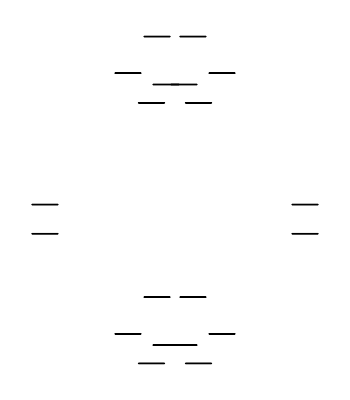
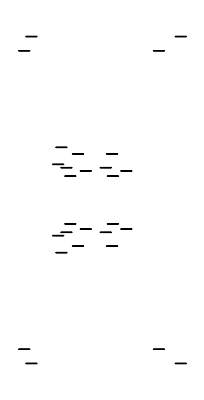
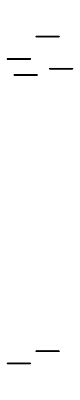
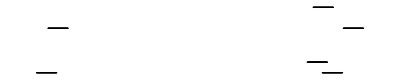
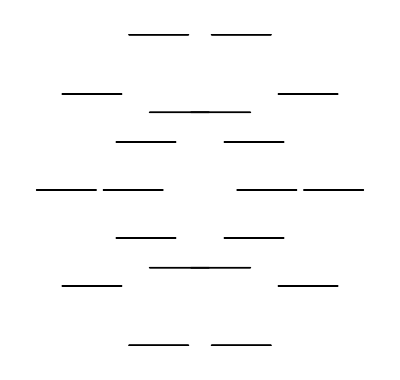
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,Show[{}]}

```mathematica
Show[#]&/@Pobs
```